```mathematica
F[x_,k_]:=Abs[1.0*(1/x-1/2*Cot[x/2]-Sum[(-1)^(s+1)*BernoulliB[2*s]/((2*s)!)*x^(2*s-1),{s,1,k-1}])*((((2*k)!)/BernoulliB[2*k])*Sin[x]*x^(-2*k))]
```

```mathematica
F[4.2,100]
```

4.68599×10^18

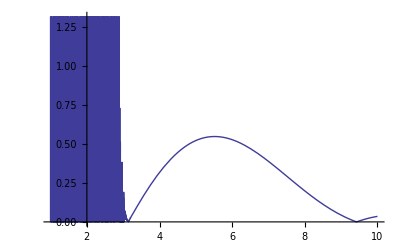

```mathematica
Plot[F[x,25],{x,1,10}]
```

```mathematica
G[x_,k_]:=1.0*(1/x-1/2*Cot[x/2]-Sum[(-1)^(s+1)*BernoulliB[2*s]/((2*s)!)*x^(2*s-1),{s,1,k-1}])
```

```mathematica
G[100,1000]
```

-3.46234974369396×10^2399

```mathematica
F[u_,k_]:=1.0*(1/u-1/2*Cot[u/2]-Sum[Abs[BernoulliB[2*j]]/((2*j)!)*u^(2*j-1),{j,1,k}])*((2*k+2)!)/BernoulliB[2*k+2]*Sin[u]*u^(-2*k-1)
```

```mathematica
F[1.2,11]
```

-6.99588

```mathematica
Sum[(-1)^n*BernoulliB[2*n]/((2*n)!)*x^(2*n-1),{n,1,Infinity}]
```

(-2+x Cot[x/2])/(2 x)

```mathematica
Assuming[k>1&&k ∈Integers,Integrate[t^(2*13)/(E^(2*Pi*t)-1),{t,0,Infinity}]]
```

(48076088562799171875 Zeta[27])/(16 π^27)

```mathematica
F[k_]:=-1/2 Csc[k π] Zeta[-2 k]-(2 π)^(-1-2 k) (2 k)! Zeta[1+2 k]
```

```mathematica
F[3]
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
Gamma[4]
```

6

```mathematica
F[k_]:=(2*Pi)^(-2*k-1)*(2*k)!*Zeta[2*k+1]
```

```mathematica
F[13]
```

(48076088562799171875 Zeta[27])/(16 π^27)